# “Hump-backed plateau”

/Users/gianmicheleinnocenti/Desktop/parton-shower-simulator/Kernel/PartonShowerMCFull.wl

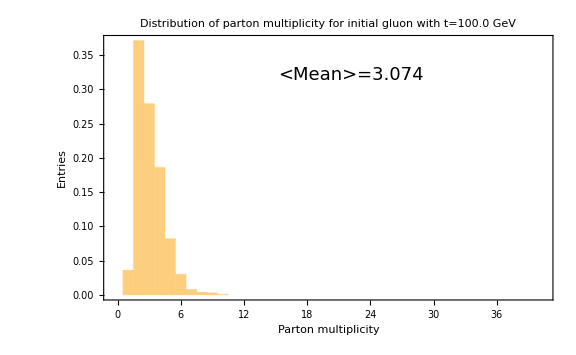
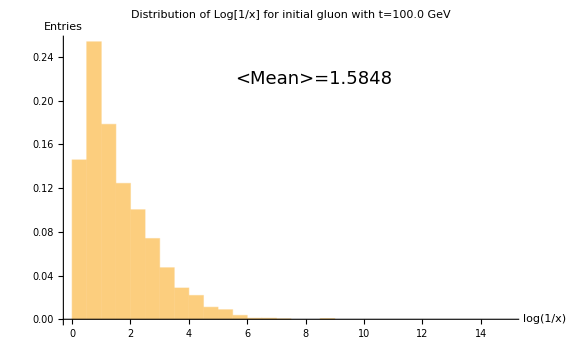
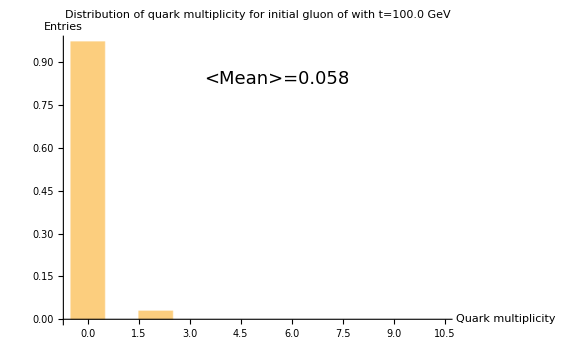

```mathematica
pathpackage="/Users/gianmicheleinnocenti/Desktop/parton-shower-simulator";
Clear[kernelpath,notebookpath];
kernelpath = StringJoin[pathpackage,"/Kernel"];
resultspath = StringJoin[pathpackage,"/Notebooks/plots"];
pathmain = StringJoin[kernelpath,"/PartonShowerMCFull.wl"]
SetDirectory[kernelpath];
<<"PartonShowerMCFull.wl"
SilentErrors[];
SetStandardSeeds[];
resultspath = StringJoin[pathpackage,"/Notebooks/plots/plotsNTonlygtogg_"];
vactivatedebug = 0;
vnevents = 1000;
vtscaleptinit =100.;
vtscalecutoff = 1;
vmaxiteration = 200; (* just a satefy tool to avoid infinite loops, value is not meaningful*)
vactivateqqbar = 1;
veffectivemassquark = 1.5;
RunShowerMulti[vnevents,vtscaleptinit,vtscalecutoff,SudakovPgtoggvacuum,SudakovPgtoqqbarvacuum,Pgtoggvacuum,Pgtoqqbarvacuum,Pgtoggvacuumsymmetric,Pgtoqqbarvacuum,
                               vactivatedebug,vmaxiteration,vactivateqqbar,veffectivemassquark,resultspath]
```

/Users/gianmicheleinnocenti/Desktop/parton-shower-simulator/Kernel/PartonShowerMCFull.wl

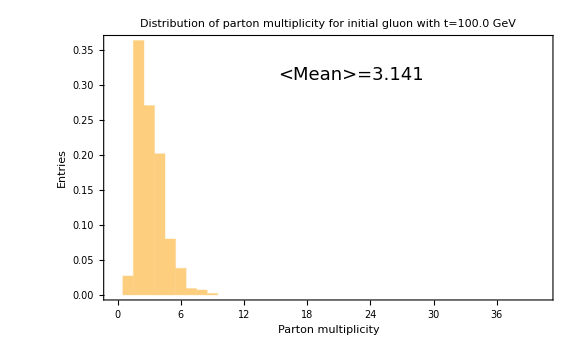
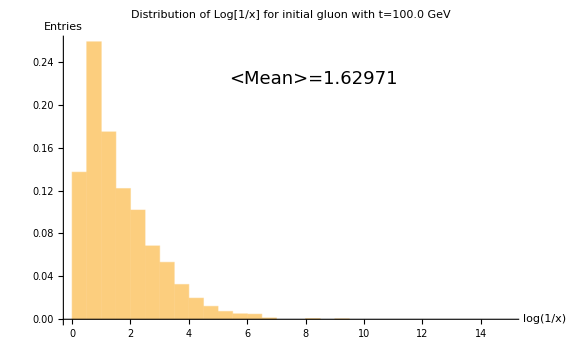
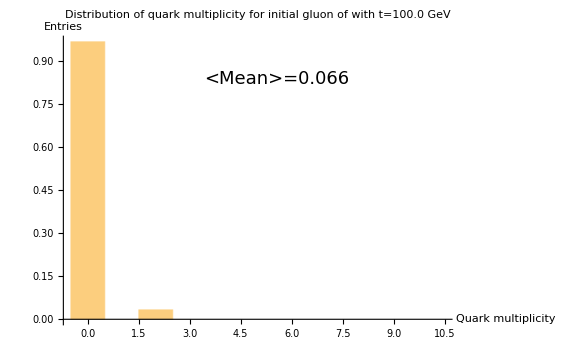

```mathematica
pathpackage="/Users/gianmicheleinnocenti/Desktop/parton-shower-simulator";
Clear[kernelpath,notebookpath];
kernelpath = StringJoin[pathpackage,"/Kernel"];
resultspath = StringJoin[pathpackage,"/Notebooks/plots"];
pathmain = StringJoin[kernelpath,"/PartonShowerMCFull.wl"]
SetDirectory[kernelpath];
<<"PartonShowerMCFull.wl"
SilentErrors[];
SetStandardSeeds[];
resultspath = StringJoin[pathpackage,"/Notebooks/plots/plotsNTonlygtogg_"];
vactivatedebug = 0;
vnevents = 1000;
vtscaleptinit =100.;
vtscalecutoff = 1;
vmaxiteration = 200; (* just a satefy tool to avoid infinite loops, value is not meaningful*)
vactivateqqbar = 1;
veffectivemassquark = 1.5;
RunShowerMulti[vnevents,vtscaleptinit,vtscalecutoff,SudakovPgtoggvacuumNTQ2Medium1,SudakovPgtoqqbarvacuum,Pgtoggmedium1,Pgtoqqbarvacuum,Pgtoggmedium1symmetric,Pgtoqqbarvacuum,
                               vactivatedebug,vmaxiteration,vactivateqqbar,veffectivemassquark,resultspath]
```